```mathematica
SetDirectory[DirectoryName[ToFileName["FileName"/.NotebookInformation[SelectedNotebook[]]]]]
```

/Users/ttesileanu/Documents/research/bio/crispr/crispr_fitness

# Matching experimental spacer abundances to spacer effectiveness or acquisition rate

In order to take advantage of intuition from actual data, it’s easiest to keep the model quantities expressed in real units. In this notebook I assume the following:
* time t is measured in hours
* bacterial and viral concentrations n_i, v are expressed in 10^8 individuals/ml
* the encounter rate g is expressed in units of 10^-8ml/hour
* fitness f is expressed in hour^-1
* spacer loss rate k is expressed in hour^-1
* death+acquisition rate of infected bacteria μ is expressed in hour^-1
* acquisition probabilities α are dimensionless (they show what fraction of the infected bacteria that are lost per unit time acquire spacers)
* the burst factor b is dimensionless
* failure probabilities η_i are dimensionless

## Set up the general equations

We write down the equations for a population of bacteria with either no spacer or a single spacer, in which both acquisition rate and effectiveness can vary between different spacers. Infected bacteria do not die instantly, but switch to a non-growing state with a constant death rate. Serial dilution and viral decay are also possible.

```mathematica
createEquationsGeneral[rules_]:=Module[{nsp=Evaluate[nsp/.rules]},
({
n[0]'[t]==f[0] (1-ntot/Kpop)n[0][t]+k Sum[n[i][t],{i,1,nsp}]-g η[0]v[t]n[0][t]-s[0]n[0][t],
nI[0]'[t]==g η[0] v[t]n[0][t]-μ nI[0][t]-s[0]nI[0][t],
v'[t]==b μ((1-αtot)nI[0][t]+ Sum[nI[k][t],{k,1,nsp}])-g v[t]Sum[n[k][t],{k,0,nsp}]-sv v[t]
}~Join~Table[
n[i]'[t]==f[i](1-ntot/Kpop)n[i][t]-k n[i][t]+μ α[i]nI[0][t]-g η[i] v[t] n[i][t]-s[i]n[i][t]
,{i,1,nsp}]~Join~
Table[
nI[i]'[t]==g η[i] v[t] n[i][t]-μ nI[i][t]-s[i]nI[i][t],
{i,1,nsp}])/.{αtot->Sum[α[i],{i,1,nsp}],ntot->Sum[n[i][t]+nI[i][t],{i,0,nsp}]}]/.rules;
```

```mathematica
createEquations[rules_]:=createEquationsGeneral[Join[rules,Append[ Table[s[i]->0,{i,0,(nsp/.rules)}],sv->0]]];
```

## Look at single spacer dynamics

Simple test

```mathematica
sampleRules1={nsp->1,f[_]->2,b->50,μ->1,k->0.01,η[0]->1,η[1]->0.01,g->0.05,α[1]->0.01,Kpop->10^2,tmax->24};
sampleIC1={n[0][0]==10^0,n[1][0]==10^(-4),v[0]==10^1,nI[0][0]==0,nI[1][0]==0};
```

```mathematica
eqns=createEquations[sampleRules1]~Join~sampleIC1;
```

```mathematica
soln=NDSolve[eqns,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.sampleRules1)}]]~Join~{v}],{t,0,(tmax/.sampleRules1)}];
```

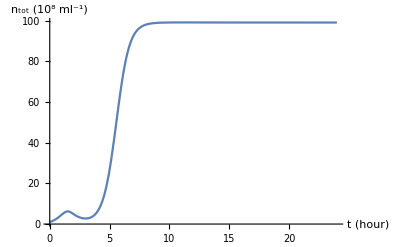

```mathematica
Plot[Evaluate[Sum[n[k][t]+nI[k][t],{k,0,(nsp/.sampleRules1)}]]/.soln,{t,0,(tmax/.sampleRules1)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

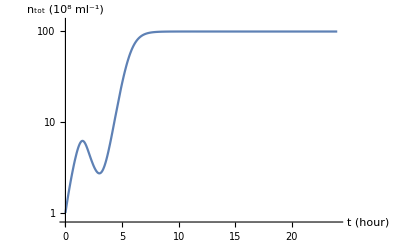

```mathematica
LogPlot[Evaluate[Sum[n[k][t]+nI[k][t],{k,0,(nsp/.sampleRules1)}]]/.soln,{t,0,(tmax/.sampleRules1)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

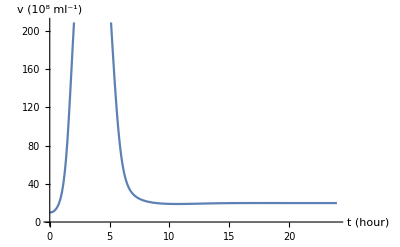

```mathematica
Plot[v[t]/.soln,{t,0,(tmax/.sampleRules1)},AxesLabel->{"t (hour)", "v (10^8 ml^-1)"}]
```

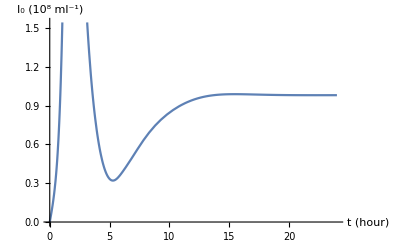

```mathematica
Plot[nI[0][t]/.soln,{t,0,(tmax/.sampleRules1)},AxesLabel->{"t (hour)", "I_0 (10^8 ml^-1)"}]
```

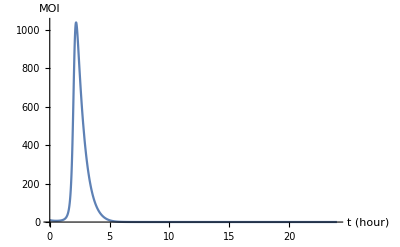

```mathematica
Plot[(v[t]/(n[0][t]+n[1][t]))/.soln,{t,0,(tmax/.sampleRules1)},PlotRange->All,AxesLabel->{"t (hour)", "MOI"}]
```

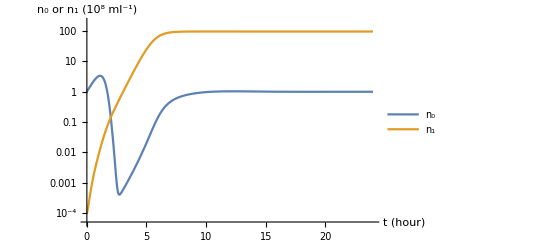

```mathematica
LogPlot[Evaluate[{n[0][t],n[1][t]}/.soln],{t,0,(tmax/.sampleRules1)},PlotRange->All,AxesLabel->{"t (hour)", "n_0 or n_1 (10^8 ml^-1)"},PlotLegends->{"n_0","n_1"}]
```

Test dynamics without infected cells

```mathematica
sampleRules2={nsp->1,f[0]->1,f[1]->0.8, b->50,k->0.001,η[0]->1,η[1]->0.0011,g->0.00001,α[1]->0.0001,Kpop->10^5,tmax->24};
sampleIC2={n[0][0]==10^4,n[1][0]==0,v[0]==10^4};
```

Some Mathematica ninja: remove the references to the infected cells, replacing them by the appropriate expression in the μ→∞ limit.

```mathematica
eqns=(Select[Normal[Series[createEquations[{nsp->1}]/.nI[k_][t]->g η[k] v[t]n[k][t]/μ,{μ,Infinity,0}]],!MatchQ[#[[1]],nI[_]'[_]]&]/.sampleRules2)~Join~sampleIC2;
```

```mathematica
soln=NDSolve[eqns,Evaluate[Table[n[k],{k,0,(nsp/.sampleRules2)}]~Join~{v}],{t,0,(tmax/.sampleRules2)}];
```

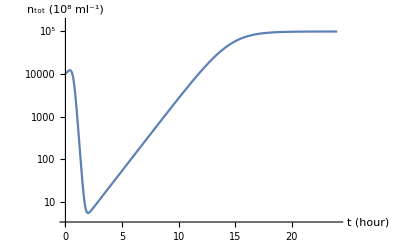

```mathematica
LogPlot[Evaluate[Sum[n[k][t],{k,0,(nsp/.sampleRules2)}]]/.soln,{t,0,(tmax/.sampleRules2)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

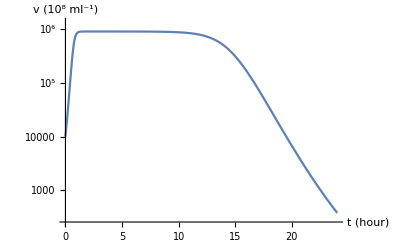

```mathematica
LogPlot[v[t]/.soln,{t,0,(tmax/.sampleRules2)},AxesLabel->{"t (hour)", "v (10^8 ml^-1)"}]
```

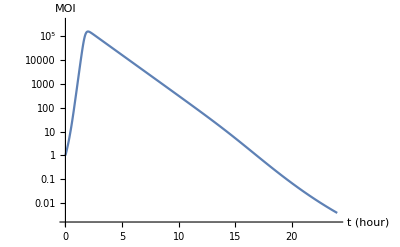

```mathematica
LogPlot[(v[t]/(n[0][t]+n[1][t]))/.soln,{t,0,(tmax/.sampleRules2)},PlotRange->All,AxesLabel->{"t (hour)", "MOI"}]
```

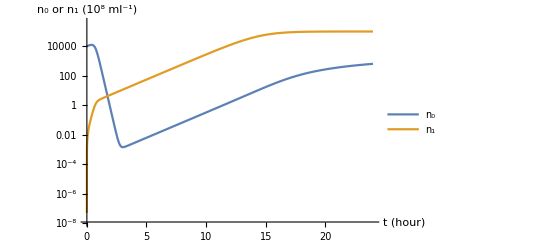

```mathematica
LogPlot[Evaluate[{n[0][t],n[1][t]}/.soln],{t,0,(tmax/.sampleRules2)},PlotRange->All,AxesLabel->{"t (hour)", "n_0 or n_1 (10^8 ml^-1)"},PlotLegends->{"n_0","n_1"}]
```

MOI increased by wildtype

Let’s first focus on experiments in which we have a mixture of wildtype and bacteria with a single spacer, and acquisition is disabled. The wildtype bacteria are useful for (temporarily) increasing the MOI, thus providing a challenge for the effectiveness of the spacer.

How much does the time at which the bacterial population start growing exponentially depend on the spacer effectiveness?

```mathematica
Clear[tmax];
noAcqDefaultRules={nsp->1,f[_]->2,b->50,μ->1,k->0.00,g->0.05,α[1]->0.00,Kpop->10^2,tmax->24,η[0]->1};
noAcqDefaultIC={n[0][0]==10^0,n[1][0]==10^(-4),v[0]==10^1,nI[0][0]==0,nI[1][0]==0};
```

```mathematica
noAcqGenerateAndSolve::usage="noAcqGenerateAndSolve[ϵvalues]
noAcqGenerateAndSolve[ηvalues,overrides]

This function generates the equations for a simulation of a mixture of wildtype bacteria with single-spacer bacteria and virus, with acquisition disabled. The second form of the command allows to override some of the default options.

The function runs one simulation for each entry in ϵvalues, representing the failure rate of the spacer. The return value contains three elements: {solns, eqns, rules}.

The first one is a list of results of NDSolve, giving the solutions for each value of η.

The second one contains the equations that are solved, in which the spacer effectiveness is left unreplaced.

The third one contains the list of rules used in the simulation, including the overrides.";
noAcqGenerateAndSolve[ηvalues_List,overrides_:{} ]:=Module[
{overridden,notoverridden,currentrules,eqns0,varlist,tmax0},
overridden=(overrides/.(A_->B_)->A);
notoverridden=Select[noAcqDefaultRules,!MemberQ[overridden, #[[1]]]&];
currentrules=notoverridden~Join~overrides;
eqns0=createEquations[currentrules]~Join~noAcqDefaultIC;
tmax0=(tmax/.currentrules);
varlist=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.currentrules)}]]~Join~{v};
solns=Map[
NDSolve[Evaluate[eqns0/.η[1]->#],varlist,{t,0,tmax0}]&,ηvalues];
{solns,eqns0,currentrules}
];
```

```mathematica
ηtotest={0.0001, 0.012, 0.02, 0.03};
ηdependence=noAcqGenerateAndSolve[ηtotest,{tmax->16}];
```

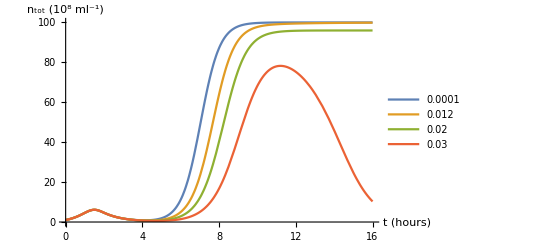

```mathematica
Plot[Evaluate[n[0][t]+n[1][t]+nI[0][t]+nI[1][t]/.ηdependence[[1]]],{t,0,(tmax/.ηdependence[[3]])},AxesLabel->{"t (hours)", "n_tot (10^8 ml^-1)"},PlotLegends->Evaluate[ηtotest]]
```

## Look at multiple spacer dynamics

```mathematica
ηRules={η[1]->0.001, η[2]->0.002,η[3]->0.003,η[4]->0.004,η[5]->0.005,η[6]->0.006,η[7]->0.007,η[8]->0.008,η[9]->0.009,η[10]->0.20};
sampleRulesMulti=Join[{nsp->10,f[_]->2,b->100,μ->1,k->0.01,η[0]->1,g->0.05,α[_]->0.01,Kpop->10^2,tmax->4096},ηRules];
nInitialRules={n[1][0]==0.06,n[2][0]==0.07,n[3][0]==0.06,n[4][0]==0.05,n[5][0]==0.04,n[6][0]==0.10,n[7][0]==0.03,n[8][0]==0.08,n[9][0]==0.06,n[10][0]==0.05};
sampleICMulti=Join[{n[0][0]==10^0,v[0]==10^1},nInitialRules,Table[nI[i][0]==0,{i, 0,(nsp/.sampleRulesMulti)}]];
```

```mathematica
eqns=createEquations[sampleRulesMulti]~Join~sampleICMulti;
```

```mathematica
soln=NDSolve[eqns,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.sampleRulesMulti)}]]~Join~{v}],{t,0,(tmax/.sampleRulesMulti)}];
```

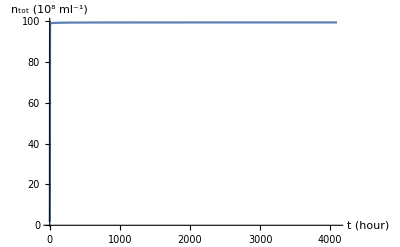

```mathematica
Plot[Evaluate[Sum[n[k][t]+nI[k][t],{k,0,(nsp/.sampleRulesMulti)}]]/.soln,{t,0,(tmax/.sampleRulesMulti)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

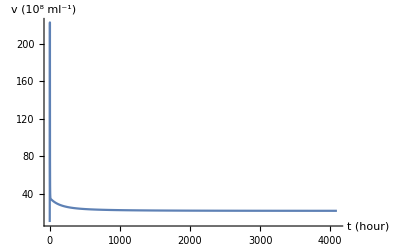

```mathematica
Plot[v[t]/.soln,{t,0,(tmax/.sampleRulesMulti)},AxesLabel->{"t (hour)", "v (10^8 ml^-1)"},PlotRange->All]
```

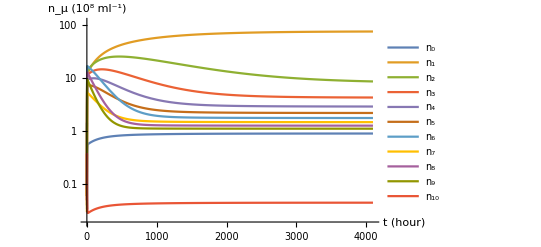

```mathematica
LogPlot[Evaluate[Table[n[i][t],{i,0,(nsp/.sampleRulesMulti)}]/.soln],{t,0,(tmax/.sampleRulesMulti)},PlotRange->All,AxesLabel->{"t (hour)", "n_μ (10^8 ml^-1)"},PlotLegends->Table[Subscript[n, i],{i,0,(nsp/.sampleRulesMulti)}]]
```

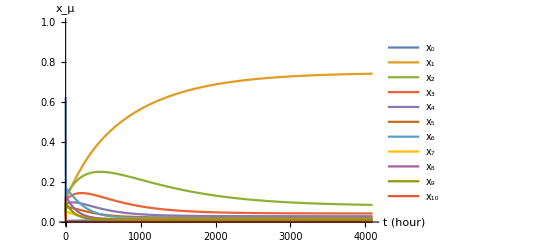

```mathematica
Plot[Evaluate[Table[n[i][t],{i,0,(nsp/.sampleRulesMulti)}]/Sum[n[k][t]+nI[k][t],{k,0,(nsp/.sampleRulesMulti)}]/.soln],{t,0,(tmax/.sampleRulesMulti)},PlotRange->{0,1},AxesLabel->{"t (hour)", "x_μ"},PlotLegends->Table[Subscript[x, i],{i,0,(nsp/.sampleRulesMulti)}]]
```

## Check population-level priming

Time to steady state with no initial spacers

We have wild type that’s completely vulnerable to viruses, a very bad spacer that only helps in 50% of encounters, and a very good spacer. The acquisition rate is the same for both spacers.

```mathematica
primingRules={nsp->2,f[_]->2,b->100,μ->1,k->0.01,η[0]->1,η[1]->0.1,η[2]->0.005,g->0.05,α[_]->0.01,Kpop->10^2,tmax->24};
primingICNoSpacers={n[0][0]==10^0,n[1][0]==0.0,n[2][0]==0.0,v[0]==10^1,nI[0][0]==0,nI[1][0]==0, nI[2][0]==0};
```

```mathematica
eqns=createEquations[primingRules]~Join~primingICNoSpacers;
```

```mathematica
soln=NDSolve[eqns,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.primingRules)}]]~Join~{v}],{t,0,(tmax/.primingRules)}];
```

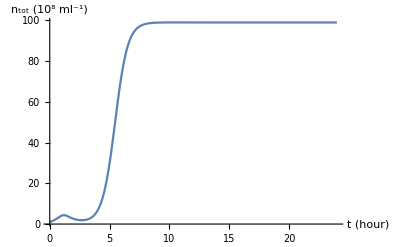

```mathematica
Plot[Evaluate[Sum[n[k][t]+nI[k][t],{k,0,(nsp/.primingRules)}]]/.soln,{t,0,(tmax/.primingRules)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

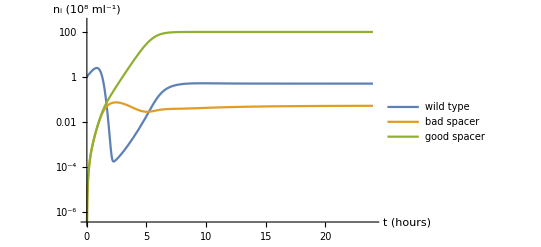

```mathematica
LogPlot[Evaluate[{n[0][t],n[1][t],n[2][t]}/.soln],{t,0,(tmax/.primingRules)},AxesLabel->{"t (hours)", "n_i (10^8 ml^-1)"},PlotLegends->{"wild type", "bad spacer", "good spacer"}]
```

How long does it take for the good spacer to reach steady state? First thought is to impose some arbitrary cutoff on the rate of change of the fraction of that spacer (compared to non-infected bacteria only), but that doesn’t work too well because of non-monotonic behavior. Instead, we put a cutoff on the square root of the sum of the squares of the first and second time derivatives of the spacer fraction.

```mathematica
goodSpacerConcentration=(n[2][#]/(n[0][#]+n[1][#]+n[2][#])&)/.soln[[1]];
goodSpacerRate=goodSpacerConcentration';
goodSpacerAcceleration=goodSpacerRate';
equilibriumThreshold = 0.0002;
```

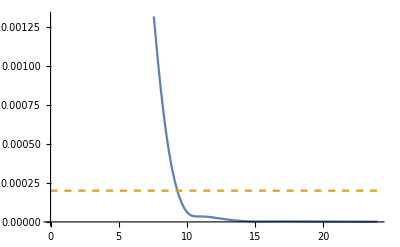

```mathematica
Plot[{Sqrt[goodSpacerRate[t]^2+goodSpacerAcceleration[t]^2],equilibriumThreshold},{t,0,(tmax/.primingRules)},PlotStyle->{ColorData[97,"ColorList"][[1]],Dashed}]
```

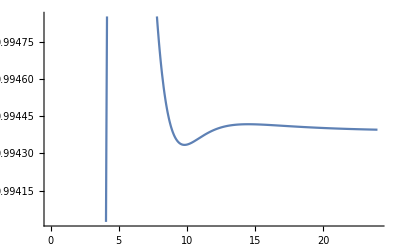

```mathematica
Plot[goodSpacerConcentration[t],{t,0,(tmax/.primingRules)}]
```

Now find the time to steady state:

```mathematica
t/.FindRoot[Sqrt[goodSpacerRate[t]^2+goodSpacerAcceleration[t]^2]==equilibriumThreshold,{t,0,(tmax/.primingRules)},Method->"Brent"]
```

9.31021

Time to steady state with initial “bad” spacer

```mathematica
primingICBadSpacers={n[0][0]==0.5,n[1][0]==0.5,n[2][0]==0.0,v[0]==10^1,nI[0][0]==0,nI[1][0]==0, nI[2][0]==0};
```

```mathematica
eqnsPrimed=createEquations[primingRules]~Join~primingICBadSpacers;
```

```mathematica
solnPrimed=NDSolve[eqnsPrimed,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.primingRules)}]]~Join~{v}],{t,0,(tmax/.primingRules)}];
```

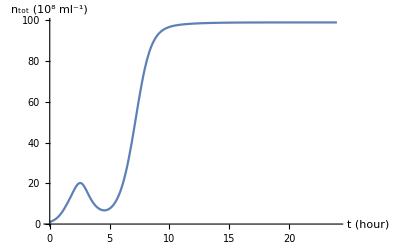

```mathematica
Plot[Evaluate[Sum[n[k][t]+nI[k][t],{k,0,(nsp/.primingRules)}]]/.solnPrimed,{t,0,(tmax/.primingRules)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

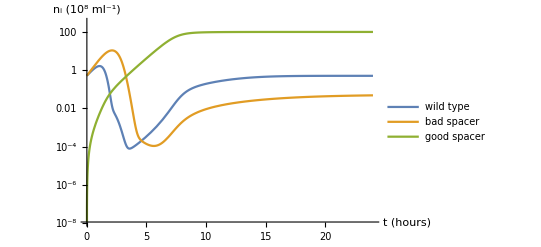

```mathematica
LogPlot[Evaluate[{n[0][t],n[1][t],n[2][t]}/.solnPrimed],{t,0,(tmax/.primingRules)},AxesLabel->{"t (hours)", "n_i (10^8 ml^-1)"},PlotLegends->{"wild type", "bad spacer", "good spacer"}]
```

```mathematica
goodSpacerConcentrationPrimed=(n[2][#]/(n[0][#]+n[1][#]+n[2][#])&)/.solnPrimed[[1]];
goodSpacerRatePrimed=goodSpacerConcentrationPrimed';
goodSpacerAccelerationPrimed=goodSpacerRatePrimed';
```

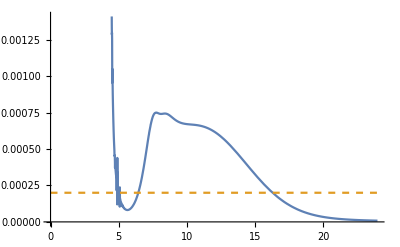

```mathematica
Plot[{Sqrt[goodSpacerRatePrimed[t]^2+goodSpacerAccelerationPrimed[t]^2],equilibriumThreshold},{t,0,(tmax/.primingRules)},PlotStyle->{ColorData[97,"ColorList"][[1]],Dashed}]
```

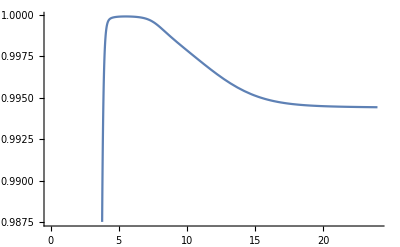

```mathematica
Plot[goodSpacerConcentrationPrimed[t],{t,0,(tmax/.primingRules)}]
```

```mathematica
t/.FindRoot[Sqrt[goodSpacerRatePrimed[t]^2+goodSpacerAccelerationPrimed[t]^2]==equilibriumThreshold,{t,0,(tmax/.primingRules)},Method->"Brent"]
```

16.3052

## Compare to TECAN data

Load data

```mathematica
rawTecanData=Import["../data/Overlapping 5 Test.csv"];
tecanHeader=rawTecanData[[All,1]];
tecanRows=rawTecanData[[All,2;;]];
```

```mathematica
tecanTime=rawTecanData[[2]][[2;;]];
tecanTemp=rawTecanData[[3]][[2;;]];
tecanSpacers=tecanHeader[[4;;8]];
tecanData=Transpose[Partition[tecanRows[[4;;]],5]];
```

```mathematica
Dimensions[tecanData]
```

{5,3,138}

```mathematica
tecanHeader
```

{Cycle Nr.,Time [s],Temp. [Â°C],AAGG,GTCA,GTTT,TTTT,TTTG,AAGG,GTCA,GTTT,TTTT,TTTG,AAGG,GTCA,GTTT,TTTT,TTTG}

```mathematica
Dimensions[tecanData[[1]]]
```

{3,138}

```mathematica
Dimensions[Transpose[{tecanTime,tecanData[[1,1]]}]]
```

{138,2}

Visualize the data

Look at variability between replicates.

```mathematica
tecanPlots=Table[ListPlot[Evaluate[Table[Transpose[{tecanTime/3600,tecanData[[j,i]]}],{i,1,3}]],AxesLabel->{"t (hours)","OD spacer "<>tecanSpacers[[j]]}],{j,1,Length[tecanData]}];
```

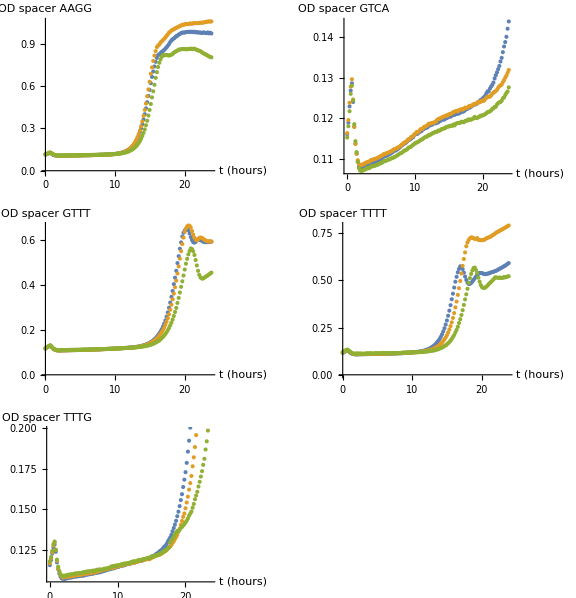

```mathematica
GraphicsGrid[Partition[Append[tecanPlots,Graphics[]],2],ImageSize->Large]
```

Let’s summarize that with mean and standard deviation, or range.

```mathematica
tecanDataMean=Mean[Transpose[tecanData]];
tecanDataStd=StandardDeviation[Transpose[tecanData]];
tecanDataLow=Min/@Transpose[#]&/@tecanData;
tecanDataHigh=Max/@Transpose[#]&/@tecanData;
```

```mathematica
plotWithError::usage="plotWithError[x, y, ylow, yhigh]
plotWithError[x, y, ylow, yhigh, plotOpts]
plotWithError[x, y, ylow, yhigh, lineOpts]

Plots y vs. x, showing an error region bounded by ylow and yhigh. plotOpts are options passed directly to the ListPlot call that draws y vs. x, while lineOpts are passed directly to the ListLinePlot that draws the error region.";
plotWithError[x_,y_,ylow_,yhigh_,plotOpts_:{},lineOpts_:{}]:=Show[ListLinePlot[Evaluate[{Transpose[{x,ylow}],Transpose[{x,yhigh}]}],Filling->{1->{2}},PlotStyle->None, Sequence@@lineOpts],
ListPlot[Evaluate[Transpose[{x,y}]],Sequence@@plotOpts]];
```

```mathematica
tecanPlotsWithErrors=Table[plotWithError[tecanTime,tecanDataMean[[j]],tecanDataLow[[j]], tecanDataHigh[[j]],{},{AxesLabel->{"t (hours)","OD spacer "<>tecanSpacers[[j]]},PlotRange->All}],{j,1,Length[tecanData]}];
```

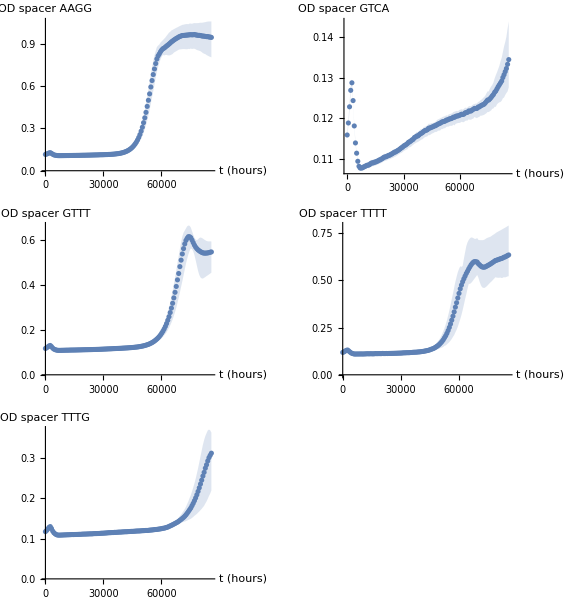

```mathematica
GraphicsGrid[Partition[Append[tecanPlotsWithErrors,Graphics[]],2],ImageSize->Large]
```

Fit the model to the data

```mathematica
expTime=tecanTime/3600.0;
expData=tecanData[[1,1]];
```

```mathematica
defaultRules={nsp->1,f[_]->2,b->50,μ->1,k->10^(-6),g->5,α[1]->0.00,Kpop->1,tmax->Max[expTime],η[0]->1,n0Initial->10^(-2),n1Initial->10^(-6),vInitial->10^(-1)};
```

We need not vary g, because this is equivalent to a rescaling of the viral population, which is not observable to us right now. For this symmetry to work, the burst size b also needs to be rescaled in the same way as the viral population, so this implies that the absolute value of the burst size is not informative, but is simply related to our choice for g.

```mathematica
ClearAll[runSimulation];
runSimulation[fitness_?NumericQ,ηvalue_?NumericQ,burst_?NumericQ,mu_?NumericQ,population_?NumericQ,wildtype_?NumericQ,spacer_?NumericQ,virus_?NumericQ]:=
Module[{
overridden={f,b,μ,Kpop,n0Initial,n1Initial,vInitial,η[1]},
notoverridden,
currentrules,
overrides,
currentIC,
eqns0,
tmax0,
varlist,
solns},
notoverridden=Select[defaultRules,!MemberQ[overridden, #[[1]]]&];
overrides={f[_]->fitness,b->burst,μ->mu,Kpop->population,n0Initial->wildtype,n1Initial->spacer,vInitial->virus,η[1]->ηvalue};
currentrules=notoverridden~Join~overrides;
currentIC={n[0][0]==n0Initial,n[1][0]==n1Initial,v[0]==vInitial,nI[0][0]==0,nI[1][0]==0}/.currentrules;
eqns0=createEquations[currentrules]~Join~currentIC;
tmax0=(tmax/.currentrules);
varlist=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.currentrules)}]]~Join~{v};
solns=NDSolve[eqns0,varlist,{t,0,tmax0}];
solns
];
```

Need to include a shift in the total population numbers to make up for possible variations in black level for the OD measurements. Also need to include an exponential growth that is observed in the experiments -- this could be the population of membrane mutants slowly taking over the bacterial community. We fix the shift by forcing the starting point of the model to coincide with the starting point of the target.

```mathematica
createObjectiveFunction[targetTime_,targetData_]:=Module[{fct},
fct[params__?NumericQ,expAmount_?NumericQ,expRate_?NumericQ]:=
Module[{solns,modelData,ntot,diff},
solns=runSimulation[params];
ntot=Sum[n[i][t]+nI[i][t],{i,0,1}]/.solns[[1]];
modelData=ntot/.({t->#}&/@targetTime);
diff=modelData-(targetData-expAmount Exp[expRate targetTime]);
diff=diff-diff[[1]];
Norm[diff]/Sqrt[Length[diff]]
];
fct
];
```

```mathematica
objFun=createObjectiveFunction[expTime,expData];
```

Need some transformations to enforce positivity and other such constraints. Unfortunately Mathematica won’t allow constraints for FindMinimum with all the methods.

```mathematica
expandParams[fitness_,ηvalue_,burst_,mu_,population_,wildtype_,spacer_,virus_,expAmount_,expRate_]:={Log[fitness],ArcTanh[2ηvalue-1],Log[burst],Log[mu],Log[population],Log[wildtype],Log[spacer],Log[virus],Log[expAmount],Log[expRate]};
restoreParams[tfitness_,tηvalue_,tburst_,tmu_,tpopulation_,twildtype_,tspacer_,tvirus_,texpAmount_,texpRate_]:={Exp[tfitness],(1+Tanh[tηvalue])/2,Exp[tburst],Exp[tmu],Exp[tpopulation],Exp[twildtype],Exp[tspacer],Exp[tvirus],Exp[texpAmount],Exp[texpRate]};
```

```mathematica
paramsToRules[f_,η_,b_,m_,p_,w_,s_,v_,eA_,eR_]:={fitness->f,ηvalue->η,burst->b,mu->m,population->p,wildtype->w,spacer->s,virus->v,expAmount->eA,expRate->eR};
rulesToParams[rules_]:={tfitness,tηvalue,tburst,tmu,tpopulation,twildtype,tspacer,tvirus,texpAmount,texpRate}/.rules;
```

```mathematica
expandParamList[params_List]:=Module[
{depth=Length[params[[1]]]-1,transformed},
transformed=Table[expandParams@@params[[;;,i+1]],{i,1,depth}];
Table[Prepend[transformed[[;;,i]],params[[i]][[1]]],{i,1,Length[params]}]
];
```

```mathematica
compressedObjFun=objFun@@restoreParams[##]&;
```

```mathematica
bestFitParamsRaw=FindMinimum[compressedObjFun[tfitness,tηvalue,tburst,tmu,tpopulation,twildtype,tspacer,tvirus,texpAmount,texpRate],
Evaluate[expandParamList[{{tfitness,1.3},{tηvalue,0.0215},{tburst,50.0},{tmu,1.0},{tpopulation,0.95},{twildtype,0.02},{tspacer,10.0^(-7)},{tvirus,0.2},{texpAmount,0.2},
{texpRate,0.001}}]],WorkingPrecision->30]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.0754122.

InterpolatingFunction::dmval: Input value {0.174111} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.0754122.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 30. digits of working precision to meet these tolerances.

{0.139091156472537613719708815552,{tfitness→0.262364264467491059562576083408,tηvalue→-2.00801934519273164000639862099,tburst→2.91045833631164100383194715091,tmu→-0.794268100472281027290290260862,tpopulation→-0.262322487180804820998019600964,twildtype→-2.55280526510437565621622347248,tspacer→-16.737892621506664622194706827,tvirus→-2.76217876725214689997356021076,texpAmount→-1.59458481997325775154158611688,texpRate→-6.89260838319564106887708152737}}

```mathematica
bestFitParams={bestFitParamsRaw[[1]],paramsToRules@@restoreParams@@rulesToParams[bestFitParamsRaw[[2]]]}
```

{0.139091156472537613719708815552,{fitness→1.30000000000000000978520412549,ηvalue→0.017705102516836742360812683875,burst→18.365214082787573842943333743,mu→0.451911867995494409639619671917,population→0.769262906276437865540625743102,wildtype→0.07786293317345633305910381867,spacer→5.380536672469032708419090035×10^-8,virus→0.063154020442225110901851281736,expAmount→0.20299278956137793621910144433,expRate→0.0010152621914005080632743356281}}

Here’s the best I could do by hand:

```mathematica
bestFitParams={None,{fitness->1.3,ηvalue->0.0215,burst->50,mu->1,population->0.95,wildtype->2 10^(-2),spacer->10^(-7),virus->0.2,expAmount->0.2,expRate->0.001}};
```

```mathematica
bestFitSolns=runSimulation[fitness,ηvalue,burst,mu,population,wildtype,spacer,virus]/.bestFitParams[[2]];
```

```mathematica
expr[t_]:=Sum[n[i][t]+nI[i][t],{i,0,1}]+expAmount Exp[expRate t];
```

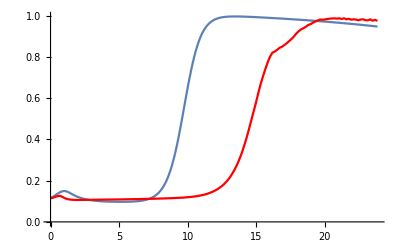

```mathematica
Show[Plot[Evaluate[(expr[t]-expr[0]+expData[[1]])/.bestFitSolns/.bestFitParams[[2]]],{t,0,(tmax/.defaultRules)}],ListPlot[Transpose[{expTime,expData}],Joined->True,PlotStyle->Red]]
```

## Check analytical calculations for single protospacer problem

Defining the equations

```mathematica
eqns0={
n0'[t]==f0(1-n[t]/Kpop)n0[t]+k n1[t]-g v[t] n0[t],
I0'[t]==g v[t] n0[t]-μ I0[t],
n1'[t]==f1(1-n[t]/Kpop)n1[t]-k n1[t]-g η v[t]n1[t]+α μ I0[t],
I1'[t]==g η v[t]n1[t]-μ I1[t],
v'[t]==b(1-α)μ I0[t]+ b μ I1[t]- g v[t](n0[t]+n1[t])
};
```

```mathematica
nTotRule={n->(n0[#]+I0[#]+n1[#]+I1[#]&)};
aRule={α->1-a};
eqns=eqns0/.aRule;
```

```mathematica
eqnsRules=eqns/.(A_==B_)->(A->B)
```

{n0'[t]→f0 (1-n[t]/Kpop) n0[t]+k n1[t]-g n0[t] v[t],I0'[t]→-μ I0[t]+g n0[t] v[t],n1'[t]→(1-a) μ I0[t]-k n1[t]+f1 (1-n[t]/Kpop) n1[t]-g η n1[t] v[t],I1'[t]→-μ I1[t]+g η n1[t] v[t],v'[t]→a b μ I0[t]+b μ I1[t]-g (n0[t]+n1[t]) v[t]}

Compare to result from createEquations

```mathematica
eqnsAgain=createEquations[{nsp->1,η[0]->1,η[1]->η}]/.n[0]->n0/.nI[0]->I0/.n[1]->n1/.nI[1]->I1/.f[0]->f0/.f[1]->f1/.α[1]->α;
```

```mathematica
ShouldBeTrue=eqnsAgain/.(eqnsRules/.nTotRule)/.aRule//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqns/.nTotRule/.(eqnsAgain/.(A_==B_)->(A->B))/.aRule//Simplify
```

{True,True,True,True,True}

Checking differential equation for n(t)

This is our analytical result for n'(t):

```mathematica
ourNOde=(f0 n0[t]+f1 n1[t])(1-n[t]/Kpop)-μ a I0[t]-μ I1[t];
```

```mathematica
ShouldBeZero=(n0'[t]+I0'[t]+n1'[t]+I1'[t]/.eqnsRules)-ourNOde//Simplify
```

0

Checking the steady-state analytical results

```mathematica
eqnsSteady=eqns/.f_'->(0&)/.f_[t]->f
```

{0==f0 (1-n/Kpop) n0+k n1-g n0 v,0==g n0 v-I0 μ,0==-k n1+f1 (1-n/Kpop) n1-g n1 v η+(1-a) I0 μ,0==g n1 v η-I1 μ,0==-g (n0+n1) v+a b I0 μ+b I1 μ}

```mathematica
calFRule={n->Kpop(1-calF)};
```

Here are some expressions we get analytically.

```mathematica
vRule1={v->1/g(f0 calF+k (b a - 1)/(1-b η))};
```

```mathematica
n0Rule1={n0->(μ(1-b η))/(b μ(a-η)+(f0 calF + k (b a - 1)/(1-b η))(1-η-η b (1-a)))n};
n0Rule2={n0->(1-b η)/(b(a-η)+(g v)/μ(1-η-η b(1-a)))n};
n1Rule1={n1->(b a - 1)/(1-b η)n0};
```

```mathematica
I0Rule={I0->(g v n0)/μ};
I1Rule={I1->(g η v n1)/μ};
```

```mathematica
calFRule1={calF->k/f0 1/(1-b η)(b a - 1)/(b-1+(f1/f0-1)(b a-1)/(a-η))};
calFRule2={calF->k/f0(a-η)/(1-b η)(b a - 1)/(1-a-η(b-1)+f1/f0(b a-1))};
```

```mathematica
ShouldBeTrue=eqnsSteady/.I0Rule/.I1Rule/.n1Rule1/.n0Rule1/.calFRule/.vRule1/.calFRule1//Simplify//Expand//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqnsSteady/.I0Rule/.I1Rule/.n1Rule1/.n0Rule1/.calFRule/.vRule1/.calFRule2//Simplify//Expand//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqnsSteady/.I0Rule/.I1Rule/.n1Rule1/.n0Rule2/.calFRule/.vRule1/.calFRule1//Simplify//Expand//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeZero=(n0/.n0Rule1)-(n0/.n0Rule2/.vRule1)//Simplify
```

0

Critical value of η

```mathematica
ηcEquation=Collect[Assuming[a≠η,k(b a - 1)/(b f0 (b-1))((a-η)/calF-(a-η)/.calFRule1/.f1->(1+ϵ) f0//Simplify)],η,Collect[Simplify[#],ϵ,Simplify]&]
```

(a ((-1+b) f0+k-a b k))/((-1+b) b f0)+((-1+a b) ϵ)/((-1+b) b)+((-(-1+b) (1+a b) f0+(-1+a b) k)/((-1+b) b f0)+((1-a b) ϵ)/(-1+b)) η+η^2

```mathematica
ηcRootRules=Assuming[a>η&&a>1/b&&η<1/b&&a>0&&b>1&&f0>0&&k>0,Solve[ηcEquation==0,η]//Simplify]
```

{{η→1/(2 (-1+b) b f0)(f0 (-1+a b^2 (1+ϵ)-b (-1+a+ϵ))-(-1+a b) (k+√(k^2-2 f0 k (1+b (-1+ϵ))+f0^2 (-1+b+b ϵ)^2)))},{η→1/(2 (-1+b) b f0)(f0 (-1+a b^2 (1+ϵ)-b (-1+a+ϵ))+(-1+a b) (-k+√(k^2-2 f0 k (1+b (-1+ϵ))+f0^2 (-1+b+b ϵ)^2)))}}

```mathematica
ηcExpansion=Assuming[b>1&&f0>0&&k>0,Series[η/.ηcRootRules,{ϵ,0,4}]//Simplify];
```

The second solution can be ignored since it is η_c>a, which is unlikely to be true in any realistic conditions.

```mathematica
ηcExpansionPaper={ηc->1/b(1-k/f0(b a - 1)/(b-1))+ϵ (k (b a - 1))/f0 1/((b-1)(b-1+k/f0))-ϵ^2(k (b a - 1))/f0 b/(b-1+k/f0)^3+ϵ^3(k (b a - 1))/f0(b^2(b-1-k/f0))/(b-1+k/f0)^5-ϵ^4(k (b a - 1))/f0(b^3((b-1)^2-3(b-1)k/f0+(k/f0)^2))/(b-1+k/f0)^7};
```

```mathematica
shouldBeZero=(ηc/.ηcExpansionPaper)-Normal[ηcExpansion[[1]]]//Simplify
```

0

```mathematica
ηcExpansionAlt={ηc->1/b-k/f0(b a - 1)/(b (b-1))(1-ϵ b 1/(b-1+k/f0)+(ϵ b)^2(b-1)/(b-1+k/f0)^3-(ϵ b)^3((b-1)(b-1-k/f0))/(b-1+k/f0)^5+(ϵ b)^4((b-1)((b-1)^2-3(b-1)k/f0+(k/f0)^2))/(b-1+k/f0)^7)};
```

```mathematica
shouldBeZero=(ηc/.ηcExpansionAlt)-Normal[ηcExpansion[[1]]]//Simplify
```

0

What happens when b>>1? Let’s write everything in terms of the product η b.

```mathematica
ηbEquation=Collect[b^2 ηcEquation/.η->ηb/b,ηb,Collect[Simplify[#],ϵ,Simplify]&]
```

(a b ((-1+b) f0+k-a b k))/((-1+b) f0)+(b (-1+a b) ϵ)/(-1+b)+((-(-1+b) (1+a b) f0+(-1+a b) k)/((-1+b) f0)+((b-a b^2) ϵ)/(-1+b)) ηb+ηb^2

```mathematica
ηbSolnLargeB=ηb/.Solve[Normal[Series[ηbEquation,{b,Infinity,-1}]//Simplify]==0,ηb][[1]]//Simplify
```

(f0-a k+f0 ϵ)/(f0+f0 ϵ)

```mathematica
ShouldBeZero=ηbSolnLargeB-(1-k/f0 a/(1+ϵ))//Simplify
```

0

```mathematica
ηbEquationNoR=Series[((a-η)/calF-(a-η)/.calFRule1/.η->ηb/b//Simplify),{b,Infinity,0}]
```

(f1-a k-f1 ηb)/k+O[1/b]^1

```mathematica
ηbSolnLargeBNoR=ηb/.Solve[Normal[ηbEquationNoR]==0,ηb][[1]];
```

```mathematica
ShouldBeZero=ηbSolnLargeBNoR-(1-(k a)/f1)//Simplify
```

0

```mathematica
Assuming[f0>0&&ϵ>-1,(Series[b η/.ηcRootRules[[1]],{b,Infinity,1}]//Simplify)/.ϵ->f1/f0-1//Simplify]
```

(1-(a k)/f1)+(k (f1^2-a (f0 (f1-k)+f1 k)))/(f1^3 b)+O[1/b]^2

Rederiving analytical solution

```mathematica
rederiveIEqns=Solve[eqnsSteady[[{2,4}]],{I0,I1}][[1]]
```

{I0→(g n0 v)/μ,I1→(g n1 v η)/μ}

```mathematica
rederiveN1Rule1=Solve[eqnsSteady[[1]]/.calFRule,n1][[1]]//Simplify
```

{n1→(-calF f0 n0+g n0 v)/k}

```mathematica
rederiveVRule=Solve[Assuming[v≠0&&n0≠0,eqnsSteady[[5]]/.rederiveIEqns/.rederiveN1Rule1//Simplify],v][[1]]//Simplify
```

{v→(calF f0-k+a b k-b calF f0 η)/(g-b g η)}

```mathematica
rederiveN1Rule2=(rederiveN1Rule1/.rederiveVRule)//Simplify
```

{n1→(n0-a b n0)/(-1+b η)}

```mathematica
rederiveCalFRule=Solve[Assuming[n0≠0,eqnsSteady[[3]]/.calFRule/.rederiveIEqns/.rederiveN1Rule1/.rederiveVRule//Simplify],calF][[1]]
```

{calF→((-1+a b) k (a-η))/((-1+b η) (-f0+a f0+f1-a b f1-f0 η+b f0 η))}

```mathematica
rederiveN0Rule=Solve[(1-(n0+I0+n1+I1)/Kpop==calF/.rederiveIEqns/.rederiveN1Rule1)//Simplify,n0][[1]]/.rederiveVRule//Simplify
```

{n0→((-1+calF) Kpop (-1+b η)^2 μ)/(-(-1+a b) k (1+(-1+(-1+a) b) η)+calF f0 (-1+b η) (1+(-1+(-1+a) b) η)+b (a-η) (-1+b η) μ)}

Checking matching between rederived solution and the one we had

```mathematica
ShouldBeZero=(I0/.rederiveIEqns)-(I0/.I0Rule)//Simplify
```

0

```mathematica
ShouldBeZero=(I1/.rederiveIEqns)-(I1/.I1Rule)//Simplify
```

0

```mathematica
ShouldBeZero=(calF/.calFRule1)-(calF/.rederiveCalFRule)//Simplify
```

0

```mathematica
ShouldBeZero=(v/.rederiveVRule)-(v/.vRule1)//Simplify
```

0

```mathematica
ShouldBeZero=(n1/.n1Rule1)-(n1/.rederiveN1Rule2)//Simplify
```

0

```mathematica
ShouldBeZero=(n1/.n1Rule1)-(n1/.rederiveN1Rule1/.vRule1)//Simplify
```

0

```mathematica
ShouldBeZero=(n0/.rederiveN0Rule)-(n0/.n0Rule1/.calFRule)//Simplify
```

0

When there is no spacer loss

```mathematica
ShouldBeZero=(n0/n/.n0Rule1/.calFRule/.calFRule1/.k->0)-(1-b η)/(b(a-η))//Simplify
```

0

```mathematica
ShouldBeZero=(n1/n/.n1Rule1/.n0Rule1/.calFRule/.calFRule1/.k->0)-(b a - 1)/(b(a-η))//Simplify
```

0

```mathematica
ShouldBeZero=v/.vRule1/.calFRule1/.k->0//Simplify
```

0

When there is no self-targeting, f_1=f_0

```mathematica
ShouldBeZero=(calF/.calFRule1/.f1->f0)-k/f0 1/(1-b η)(b a-1)/(b-1)//Simplify
```

0

```mathematica
ShouldBeZero=(g v/.vRule1)-calF b f0/.calFRule1/.f1->f0//Simplify
```

0

```mathematica
ShouldBeZero=((n0/n/.n0Rule1/.calFRule)-(μ/b(1-b η)/(μ(a-η)+f0 calF(1-η-η b(1-a)))))/.calFRule1/.f1->f0//Simplify
```

0

```mathematica
ShouldBeZero=((n1/n/.n1Rule1/.n0Rule1/.calFRule)-(μ/b(b a-1)/(μ(a-η)+f0 calF(1-η-η b(1-a)))))/.calFRule1/.f1->f0//Simplify
```

0

Check n_i+I_i steady state

```mathematica
ShouldBeZero=(n0+I0/.I0Rule/.n0Rule2)-((1-b η)/(b(a-η)-(g v)/(g v + μ)(1-η)(b a-1))n)//Simplify
```

0

```mathematica
ShouldBeZero=(n1+I1/.I1Rule/.n1Rule1/.n0Rule2)-((b a-1)/(b(a-η)+(g v)/(η g v + μ)(1-η)(1-b η))n)//Simplify
```

0

## Check analytical calculations for multiple spacer case

Steady state

```mathematica
testAnalyticalSolution[ns_]:=
Module[{eqns=createEquations[{nsp->ns,η[0]->1}]/.A_'[t]->0/.A_[t]->A,
n0Rule1,nIRules,η1ηbarRule,f1fbarRule,n1nsumRule,α1aRule,vRule1,calFRule1,calFRule2,n0Rule2,calFRule3,n0Rule3,nsumRule,otherNRules},
n0Rule1=Solve[eqns[[1]]/.nI[0]->Kpop(1-calF)-n[0]-Sum[n[i]+nI[i],{i,1,ns}],n[0]][[1]];
nIRules=Prepend[Table[Solve[eqns[[ns+3+i]],nI[i]][[1]][[1]],{i,1,ns}],
Solve[eqns[[2]],nI[0]][[1]][[1]]];
η1ηbarRule={η[1]->1/n[1](ηbar Sum[n[i],{i,1,ns}]-Sum[η[j]n[j],{j,2,ns}])};
f1fbarRule={f[1]->1/n[1](fbar Sum[n[i],{i,1,ns}]-Sum[f[j]n[j],{j,2,ns}])};
n1nsumRule={n[1]->nsum-Sum[n[j],{j,2,ns}]};
α1aRule={α[1]->1-a-Sum[α[j],{j,2,ns}]};
vRule1=Solve[Assuming[nsum≠0&&g≠0&&v≠0,eqns[[3]]/.nIRules/.n0Rule1/.η1ηbarRule/.n1nsumRule/.α1aRule//Simplify],v][[1]]//Simplify;
n0Rule2=Simplify[n0Rule1/.vRule1/.n1nsumRule];
calFRule1={Kpop->Sum[n[ν]+nI[ν],{ν,0,ns}]/(1-calF)};
calFRule2=Solve[Assuming[fbar≠0&&nsum≠0&&μ≠0&&Kpop≠0,0==(Plus@@(eqns[[4;;3+ns]]/.(0==B_)->B))/.calFRule1/.nIRules/.η1ηbarRule/.
f1fbarRule/.n1nsumRule/.α1aRule/.n0Rule2/.vRule1//Simplify],calF][[1]]//Simplify;
calFRule3=Solve[v==(v/.vRule1),calF][[1]]//Simplify;
nsumRule=Solve[n[0]==(n[0]/.n0Rule2),nsum][[1]];
n0Rule3=Solve[((n[0]+nI[0]+Sum[n[i]+nI[i],{i,1,ns}]==ntot)/.nIRules/.η1ηbarRule/.n1nsumRule/.α1aRule/.nsumRule/.calFRule3//Simplify),n[0]][[1]]//Simplify;
otherNRules=Table[Solve[eqns[[3+i]]/.calFRule1/.nIRules,n[i]][[1]][[1]],{i,1,ns}];
{(n[0]/.n0Rule1)-k/(g v-f[0] calF)Sum[n[i],{i,1,ns}],
(nI[0]/.nIRules)-(g v n[0])/μ}~Join~
Table[(nI[i]/.nIRules)-(η[i] g v n[i])/μ,{i,1,ns}]~Join~{
Simplify[(g v/.vRule1)-f[0] calF-k (a b-1)/(1-b ηbar)],
Simplify[(n[0]/.n0Rule1/.vRule1)-(1-b ηbar)/(a b-1)Sum[n[i],{i,1,ns}]],
Simplify[(calF/.calFRule2)-(k/f[0] (b a-1)/(1-b ηbar)1/((b-1)+(fbar/f[0]-1)(b a-1)/(a-ηbar)))],
Simplify[(n[0]/.n0Rule3)-(1-b ηbar)/(b(a-ηbar)+g v (1-ηbar-ηbar b(1-a))/μ)ntot]
}~Join~Table[
(n[i]/.otherNRules)-(α[i] g v)/(k + η[i] g v-f[i]calF)n[0],{i,1,ns}]~Join~Table[
Simplify[(n[i]/.otherNRules/.vRule1)-α[i](k (b a-1)/(1-b ηbar)+f[0]calF)/(k (1+η[i] (b a-1)/(1-b ηbar))-f[0]calF(f[i]/f[0]-η[i]))n[0]],{i,1,ns}]];
```

```mathematica
ShouldBeZero=testAnalyticalSolution[1]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[2]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[3]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[4]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[6]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[7]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[8]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[9]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[10]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Equation for n_total

```mathematica
testAnalyticalNtotal[ns_]:=Module[{eqnsRules=createEquations[{nsp->ns,η[0]->1}]/.(A_==B_)->(A->B),ntotRule,f1fbarRule,n1nsumRule,nI1nIsumRule,α1aRule},
ntotRule={Kpop->Kpop Sum[n[ν][t]+nI[ν][t],{ν,0,ns}]/ntot[t]};
f1fbarRule={f[1]->1/(n[1][t])(fbar Sum[n[i][t],{i,1,ns}]-Sum[f[j]n[j][t],{j,2,ns}])};
n1nsumRule={n[1][t]->nsum[t]-Sum[n[j][t],{j,2,ns}]};
nI1nIsumRule={nI[1][t]->nIsum[t]-Sum[nI[j][t],{j,2,ns}]};
α1aRule={α[1]->1-a-Sum[α[j],{j,2,ns}]};
(Sum[n[ν]'[t]+nI[ν]'[t],{ν,0,ns}]/.eqnsRules/.ntotRule/.f1fbarRule/.n1nsumRule/.nI1nIsumRule/.α1aRule//Simplify)-((1-ntot[t]/Kpop)(f[0]n[0][t]+fbar nsum[t])-μ a nI[0][t]-μ nIsum[t])//Simplify
];
```

```mathematica
ShouldBeZero=Table[testAnalyticalNtotal[n],{n,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

## Check analytical calculations for serial dilution case

Doing this only for the case of a single protospacer.

Defining the equations

```mathematica
eqnsDilution={
n0'[t]==(f0(1-n[t]/Kpop)-sb)n0[t]+k n1[t]-g n0[t] v[t],
n1'[t]==(f1(1-n[t]/Kpop)-sb)n1[t]-k n1[t]-g η n1[t] v[t] + α μ I0[t],
I0'[t]==g n0[t] v[t]-μ I0[t]-sb I0[t],
I1'[t]==g η n1[t] v[t] - μ I1[t] - sb I1[t],
v'[t]==b(μ (1-α) I0[t]+μ I1[t])-g v[t](n0[t]+n1[t])-sv v[t]
};
```

```mathematica
nTotRule={n->(n0[#]+I0[#]+n1[#]+I1[#]&)};
```

```mathematica
eqnsDilutionRules=eqnsDilution/.(A_==B_)->(A->B);
```

Comparing to result from createEquationsGeneral

```mathematica
eqnsDilution0 = createEquationsGeneral[{nsp->1, η[0]->1,η[1]->η}]/.n[0]->n0/.nI[0]->I0/.n[1]->n1/.nI[1]->I1/.f[0]->f0/.f[1]->f1/.α[1]->α/.s[_]->sb;
```

```mathematica
ShouldBeTrue=eqnsDilution0/.(eqnsDilutionRules/.nTotRule)//Simplify
```

createEquationsGeneral[{nsp→1,η[0]→1,η[1]→η}]

```mathematica
ShouldBeTrue=eqnsDilution/.nTotRule/.(eqnsDilution0/.(A_==B_)->(A->B))//Simplify
```

ReplaceAll::reps: {createEquationsGeneral[{nsp→1,η[0]→1,η[1]→η}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{g n0[t] v[t]+n0'[t]==k n1[t]+n0[t] (-sb+f0 (1-(I0[t]+I1[t]+n0[t]+n1[t])/Kpop)),n1[t] (k+g η v[t])+n1'[t]==α μ I0[t]+n1[t] (-sb+f1 (1-(I0[t]+I1[t]+n0[t]+n1[t])/Kpop)),(sb+μ) I0[t]+I0'[t]==g n0[t] v[t],(sb+μ) I1[t]+I1'[t]==g η n1[t] v[t],b (-1+α) μ I0[t]+(sv+g n0[t]+g n1[t]) v[t]+v'[t]==b μ I1[t]}/.createEquationsGeneral[{nsp→1,η[0]→1,η[1]→η}]

Checking differential equation for n(t)

This is our analytical result for n'(t):

```mathematica
ourNOdeDilution=(f0 n0[t]+f1 n1[t])(1-n[t]/Kpop)-μ (1-α) I0[t]-μ I1[t]-sb n[t];
```

```mathematica
ShouldBeZero=(n0'[t]+I0'[t]+n1'[t]+I1'[t]/.eqnsDilutionRules)-ourNOdeDilution/.nTotRule//Simplify
```

0

Checking the steady-state analytical results

```mathematica
eqnsDilutionSteady=eqnsDilution/.f_'->(0&)/.f_[t]->f
```

{0==k n1+n0 (f0 (1-n/Kpop)-sb)-g n0 v,0==-k n1+n1 (f1 (1-n/Kpop)-sb)-g n1 v η+I0 α μ,0==-I0 sb+g n0 v-I0 μ,0==-I1 sb+g n1 v η-I1 μ,0==-g (n0+n1) v-sv v+b (I1 μ+I0 (1-α) μ)}

```mathematica
calFRule={n->Kpop(1-calF)};
```

```mathematica
nTotRuleSteady={n->(n0+n1+I0+I1)};
```

### When v=0

```mathematica
noVRule={v->0};
```

Here are some expressions we get analytically.

```mathematica
solnNoV1={n0->0,n1->0,I0->0,I1->0};
```

```mathematica
solnNoV2={n1->0,n0->Kpop(1-sb/f0),I0->0,I1->0};
solnNoV3={n0->Kpop (1-(sb + k)/f1)/(1+sb/k(1-f0/f1)-f0/f1),n1->Kpop ((1-(sb + k)/f1)(sb/k(1-f0/f1)-f0/f1))/(1+sb/k(1-f0/f1)-f0/f1),I0->0,I1->0};
```

```mathematica
ShouldBeTrue=eqnsDilutionSteady/.noVRule/.solnNoV1//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqnsDilutionSteady/.noVRule/.nTotRuleSteady/.solnNoV2//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqnsDilutionSteady/.noVRule/.nTotRuleSteady/.solnNoV3//Simplify
```

{True,True,True,True,True}

### When v≠0, n_0=0

This requires k=0 (otherwise n_1 and v must also be zero).

```mathematica
vRuleNoN0={v->(f1(1-n1/Kpop)-sb)/(g η(1+f1/(μ+sb)n1/Kpop))};
```

```mathematica
n1RuleNoN0={n1->sv/g 1/(b η w-1)};
```

```mathematica
wRule={w->μ/(μ+sb)};
```

```mathematica
ShouldBeTrue=eqnsDilutionSteady/.nTotRuleSteady/.{n0->0,I0->0,k->0}/.I1->(g η v)/(μ+sb)n1/.vRuleNoN0/.n1RuleNoN0/.wRule//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeZero=(v/.vRuleNoN0/.n1RuleNoN0/.wRule/.sb->0)-(f1 μ (g Kpop(b η-1)-sv))/(g η(μ g Kpop(b η-1)+f1 sv))//Simplify
```

0

### When v≠0,n_0≠0,n_1≠0

```mathematica
IRulesDilution={I0->(g v)/(μ+sb)n0,I1->(g η v)/(μ+sb)n1};
```

```mathematica
vRuleDilution1={v->((f0 n0 + f1 n1 + sb Kpop)calF-sb Kpop)/(g w ((1-α)n0+η n1))};
nRuleDilution1={n1->((b w(1-α)-1)n0-sv/g)/(1-b η w)};
```

```mathematica
vRuleDilution2={v->((f0 n0 + f1 n1)(1-(n0+n1)/Kpop)-sb(n0+n1))/(g w ((1-α)n0+η n1+(f0 n0 + f1 n1 + sb Kpop)/μ(n0+η n1)/Kpop))};
```

```mathematica
vRuleDilution3={v->(f0(1-(n0+n1)/Kpop)-sb+k n1/n0)/(g(1+f0/(μ+sb)(n0+η n1)/Kpop))};
```

```mathematica
wRule={w->μ/(μ+sb)};
```

```mathematica
ShouldBeTrue=eqnsDilutionSteady[[3;;5]]/.IRulesDilution/.calFRule/.vRuleDilution1/.nRuleDilution1/.wRule//Simplify
```

{True,True,True}

```mathematica
ShouldBeZero=(Collect[Sum[eqnsDilutionSteady[[i]]/.(A_==B_)->B,{i,1,4}],sb,Simplify]/.-n0-n1-I0-I1->-n/.calFRule//Simplify)/.IRulesDilution/.vRuleDilution1/.w->μ/(μ+sb)//Simplify
```

0

Test a different expression for the viral population.

```mathematica
ShouldBeZero=Collect[((Sum[eqnsDilutionSteady[[i]]/.(A_==B_)->(A-B),{i,1,4}]/.n->n0+n1+I0+I1//Simplify)/.IRulesDilution//Simplify),v,Simplify]/.vRuleDilution2/.wRule//Simplify
```

0

```mathematica
ShouldBeTrue=eqnsDilutionSteady[[3;;5]]/.IRulesDilution/.calFRule/.vRuleDilution2/.nRuleDilution1/.wRule//Simplify
```

{True,True,True}

And a third expression for the viral population.

```mathematica
ShouldBeTrue=eqnsDilutionSteady[[{1,3,4,5}]]/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilution3/.nRuleDilution1/.wRule//Simplify
```

{True,True,True,True}

This leaves only one equation to be satisfied -- the one that sets the value of n_0 (or, equivalently, calF).

```mathematica
(*Solve[((eqnsDilutionSteady[[1]]/.(A_==B_)->(A-B))/.n->(n0+n1+I0+I1)/.IRulesDilution/.vRuleDilution2/.nRuleDilution1/.wRule//Simplify)==0,n0]*)
```

```mathematica
(*Solve[((eqnsDilutionSteady[[2]]/.(A_==B_)->(A-B))/.n->(n0+n1+I0+I1)/.IRulesDilution/.vRuleDilution3/.nRuleDilution1/.wRule//Simplify)==0,n0]*)
```

Looks like full solution is not worth it...

### When k=0

Assuming still that v≠0,n_0≠0,n_1≠0.

```mathematica
eqnsDilutionSteadyNoLoss=eqnsDilutionSteady/.k->0;
```

```mathematica
IRulesDilution={I0->(g v)/(μ+sb)n0,I1->(g η v)/(μ+sb)n1};
```

```mathematica
vRuleDilutionNoLoss1={v->(f0 calF-sb)/g};
nRuleDilution1={n1->((b w(1-α)-1)n0-sv/g)/(1-b η w)};
```

```mathematica
wRule={w->μ/(μ+sb)};
```

```mathematica
vRuleDilutionNoLoss2={v->(f0 (1-(n0+n1)/Kpop)-sb)/(g(1+f0/(μ+sb)(n0+η n1)/Kpop))};
```

```mathematica
ShouldBeTrue=eqnsDilutionSteadyNoLoss[[{1,3,4,5}]]/.IRulesDilution/.calFRule/.vRuleDilutionNoLoss1/.nRuleDilution1/.wRule//Simplify
```

{True,True,True,True}

```mathematica
ShouldBeZero=(eqnsDilutionSteadyNoLoss[[1]]/.(A_==B_)->(A-B)/.n->n0+n1+I0+I1//Simplify)/.IRulesDilution/.vRuleDilutionNoLoss2//Simplify
```

0

```mathematica
ShouldBeTrue=eqnsDilutionSteadyNoLoss[[{1,3,4,5}]]/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilutionNoLoss2/.nRuleDilution1/.wRule//Simplify
```

{True,True,True,True}

One equation left, but I guess this also looks too messy...

```mathematica
(*Solve[(eqnsDilutionSteadyNoLoss[[2]]/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilutionNoLoss2/.nRuleDilution1/.wRule//Simplify),n0]//Simplify*)
```

### When k=0 and f_1≈f_0

#### Derive solution

Do a standard expansion of n_0 in γ=(f_1-f_0)/f_0.

```mathematica
γRule={f1->f0(1+γ)};
n0SeriesRule={n0->n0s0+γ n0s1};
```

Plug the series expansion into the remaining equation, and keep only the terms for γ^0 and γ^1.

```mathematica
lastEquationDilutionNoLossAlmostEqualGrowth=CoefficientList[Normal[Series[((eqnsDilutionSteadyNoLoss[[2]]/.(A_==B_)->(A-B)/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilutionNoLoss2/.nRuleDilution1/.wRule/.γRule//Simplify)/.n0SeriesRule//Simplify),{γ,0,1}]//Simplify],γ]
```

{-(((sv (-1+η) (sb+μ)^2+g n0s0 (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)) (-g Kpop sb (sb+μ-b η μ)+f0 (sv (sb+μ)+g (b n0s0 (-1+α+η) μ+Kpop (sb+μ-b η μ)))))/(g (sb+μ-b η μ) (g Kpop (sb+μ) (sb+μ-b η μ)-f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ))))),1/(sb+μ-b η μ)n0s1 η (sb+μ) ((b f0 (-1+α+η) μ (sv (sb+μ)+g n0s0 (sb+μ-b μ+b α μ)))/(-g Kpop (sb+μ) (sb+μ-b η μ)+f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))+((sb+μ) (sb+μ-b η μ) (-f0 sv+g Kpop (sb+μ-b μ+b α μ)) (g Kpop sb (sb+μ-b η μ)-f0 (sv (sb+μ)+g (b n0s0 (-1+α+η) μ+Kpop (sb+μ-b η μ)))))/(g Kpop (sb+μ) (sb+μ-b η μ)-f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))^2)+1/(g (sb+μ-b η μ))((f0 (sv (sb+μ)+g n0s0 (sb+μ-b μ+b α μ)) (sv (sb (-1+η)-μ) (sb+μ)-g (b n0s1 (-1+α+η) μ (sb+μ)+Kpop (sb+μ) (sb+μ-b η μ)+n0s0 (-sb^2 (-1+η)-sb (1+b (-1+α)) (-1+η) μ+b (-1+α+η) μ^2))))/(-g Kpop (sb+μ) (sb+μ-b η μ)+f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))-(g n0s1 (sb+μ)^2 (sb+μ-b η μ) (-f0 sv+g Kpop (sb+μ-b μ+b α μ)) (g Kpop sb (sb+μ-b η μ)-f0 (sv (sb+μ)+g (b n0s0 (-1+α+η) μ+Kpop (sb+μ-b η μ)))))/(g Kpop (sb+μ) (sb+μ-b η μ)-f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))^2)+α μ ((b f0 g n0s0 n0s1 (-1+α+η) μ)/(-g Kpop (sb+μ) (sb+μ-b η μ)+f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))+(n0s1 (sb+μ) (-f0 sv η+g Kpop (sb+μ-b η μ)) (g Kpop sb (sb+μ-b η μ)-f0 (sv (sb+μ)+g (b n0s0 (-1+α+η) μ+Kpop (sb+μ-b η μ)))))/(g Kpop (sb+μ) (sb+μ-b η μ)-f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))^2)}

Can use coefficient for γ^0 to find the zeroth-order solutions.

```mathematica
n0s0DilutionNoLossAlmostEqualGrowth=Solve[lastEquationDilutionNoLossAlmostEqualGrowth[[1]]==0,n0s0]//Simplify
```

{{n0s0→(g Kpop sb (sb+μ-b η μ)-f0 (sv (sb+μ)+g Kpop (sb+μ-b η μ)))/(b f0 g (-1+α+η) μ)},{n0s0→-(sv (-1+η) (sb+μ)^2)/(g (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2))}}

Now use the coefficient for γ^1 to find the first order corrections.

```mathematica
n0s1DilutionNoLossAlmostEqualGrowth1=Solve[(lastEquationDilutionNoLossAlmostEqualGrowth[[2]]/.n0s0DilutionNoLossAlmostEqualGrowth[[1]])==0,n0s1][[1]]//Simplify
```

{n0s1→-((sb (-sb+(-1+b η) μ) (-g Kpop sb (sb+μ-b μ+b α μ)+f0 (sv (sb+μ)+g Kpop (sb+μ-b μ+b α μ))) (g Kpop (-sb^2 (-1+η)-sb (1+b (-1+α)) (-1+η) μ+b (-1+α+η) μ^2)+f0 (sv (-1+η) (sb+μ)+g Kpop (sb (-1+η)+(-1+η+b α η) μ))))/(b^2 f0 g (-1+α+η)^2 μ^2 (g Kpop sb (-sb^2 (-1+η)-sb (-2+α+b (-1+α) (-1+η)+2 η) μ+(-1+b) (-1+α+η) μ^2)+f0 (sv (sb+μ) (sb (-1+η)+(-1+α+η) μ)+g Kpop (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)))))}

```mathematica
n0s1DilutionNoLossAlmostEqualGrowth2=Solve[(lastEquationDilutionNoLossAlmostEqualGrowth[[2]]/.n0s0DilutionNoLossAlmostEqualGrowth[[2]])==0,n0s1][[1]]//Simplify
```

{n0s1→-((f0 sv α μ (sb+μ)^2 (sb+μ-b η μ) (sv μ (sb (-1+α+η-α η)+(-1+α+η) μ)+g Kpop (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)))/(g (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)^2 (g Kpop sb (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)-f0 (sv (sb+μ) (sb (-1+η)+(-1+α+η) μ)+g Kpop (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)))))}

#### Check results from paper for s_b=0.

```mathematica
n0s0/.n0s0DilutionNoLossAlmostEqualGrowth/.wRule/.sb->0//Simplify
```

{(-sv+g Kpop (-1+b η))/(b g (-1+α+η)),(sv (-1+η))/((-1+b) g (-1+α+η))}

First solution corresponds to no virus -- it should have been treated above, but it doesn’t seem to have been...

This is an exact solution, not just an expansion in γ.

```mathematica
ShouldBeZero=v/.vRuleDilutionNoLoss2/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[1]]/.wRule/.sb->0//Simplify
```

0

```mathematica
ShouldBeTrue=eqnsDilutionSteadyNoLoss[[2]]/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilutionNoLoss2/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[1]]/.wRule/.sb->0//Simplify
```

True

```mathematica
ShouldBeZero=(n0+n1-Kpop)/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[1]]/.wRule/.sb->0//Simplify
```

0

```mathematica
ShouldBeZero=(n1/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[1]]/.wRule/.sb->0)-((Kpop (b(1-α)-1))/(b(1-α-η))-sv/(b g(1-α-η)))//Simplify
```

0

Second solution.

```mathematica
ShouldBeZero={(n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[2]]/.wRule/.sb->0)-(sv(1-η))/(g(b-1)(1-α-η)),
(n0s1/.n0s1DilutionNoLossAlmostEqualGrowth2/.wRule/.sb->0)-(sv α (1-b η))/(g(b-1)^2(1-α-η)^2)}//Simplify
```

{0,0}

Note that we’re treating the virus only at zeroth order here.

```mathematica
ShouldBeZero=(v/.vRuleDilutionNoLoss2/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[2]]/.wRule/.sb->0)-(f0 μ(1-α-η)((b-1)g Kpop - sv))/(g((b-1)μ g Kpop(1-α-η)+f0 sv (1-α η-η)))//Simplify
```

0

```mathematica
ShouldBeZero=((CoefficientList[Normal[Series[(n1/.nRuleDilution1/.n0->n0s0+γ n0s1),{γ,0,1}]],γ]//Simplify)/.n0s0DilutionNoLossAlmostEqualGrowth[[2]]/.n0s1DilutionNoLossAlmostEqualGrowth2/.wRule/.sb->0)-{(-sv α)/(g(b-1)(1-α-η)),(sv α (b(1-α) - 1))/(g(b-1)^2(1-α-η)^2)}//Simplify
```

{0,0}

## Check results from paper for s_v=s_b when ignoring infected cells

```mathematica
eqnsNoInfectedSteady=eqnsDilutionSteadyNoLoss[[{1,2,5}]]/.(Solve[eqnsDilutionSteadyNoLoss[[3;;4]],{I0,I1}][[1]]/.sb->0)//Simplify
```

{n0 (f0 (-1+n/Kpop)+sb+g v)==0,(f1 (Kpop-n) n1)/Kpop+g n0 v α==n1 (sb+g v η),v (sv+g (n0-b n0+n1+b n0 α-b n1 η))==0}

```mathematica
n0RuleNoInfected=Solve[eqnsNoInfectedSteady[[3]],n0][[1]]//Simplify
```

{n0→-(g n1+sv-b g n1 η)/(g-b g+b g α)}

```mathematica
vRuleNoInfected=Solve[(eqnsNoInfectedSteady[[2]]/.n->n0+n1/.n0RuleNoInfected//Simplify),v][[1]]//Simplify
```

{v→(n1 (g Kpop sb (-1+b-b α)+f1 (sv+g (Kpop (1+b (-1+α))-b n1 (-1+α+η)))))/(g Kpop (sv α+g n1 (α+η-b η)))}

```mathematica
n1ExactNoInfected=Solve[(eqnsNoInfectedSteady[[1]]/.n->n0+n1/.vRuleNoInfected/.n0RuleNoInfected//Simplify),n1]//Simplify;
```

```mathematica
n1ExactNoInfected[[1]]
```

{n1→sv/(g (-1+b η))}

### Solution with n_0=0.

```mathematica
ShouldBeZero=n0/.n0RuleNoInfected/.n1ExactNoInfected[[1]]//Simplify
```

0

```mathematica
ShouldBeZero=(n1/.n1ExactNoInfected[[1]])-sv/(g (b η-1))//Simplify
```

0

```mathematica
ShouldBeZero=(v/.vRuleNoInfected/.n1ExactNoInfected[[1]])-(f1(1-sv/(g Kpop(b η-1)))-sb)/(g η)//Simplify
```

0

### Other solutions.

Rewrite in terms of fractions.

```mathematica
nRuleNoInfected=Solve[n==(n0+n1/.n0RuleNoInfected/.n1->n x1//Simplify),n][[1]]//Simplify
```

{n→sv/(g (-1+b (1-α+x1 (-1+α+η))))}

```mathematica
ShouldBeTrue=eqnsNoInfectedSteady[[2]]/.n0RuleNoInfected/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected//Simplify
```

True

```mathematica
lastEquationNoInfectedFraction=eqnsNoInfectedSteady[[1]]/.n0RuleNoInfected/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected//Simplify
```

(sv (-1+x1) (f0 sv ((-1+x1) α+x1 η)+g Kpop (f0 (α-x1 α-x1 η)+sb (-α+x1 (-1+α+η))) (-1+b (1-α+x1 (-1+α+η)))+f1 x1 (-sv+g Kpop (-1+b (1-α+x1 (-1+α+η))))))/(g Kpop ((-1+x1) α+x1 η) (-1+b (1-α+x1 (-1+α+η))))==0

Taylor expand in γ, where f_1=f_0(1+γ).

```mathematica
γRule={f1->f0(1+γ)};
```

```mathematica
x1SeriesRule={x1->x1s0+γ x1s1};
```

```mathematica
lastEquationNoInfectedSeries=CoefficientList[Normal[Series[(lastEquationNoInfectedFraction/.(A_==B_->A-B)/.γRule/.x1SeriesRule//Simplify),{γ,0,1}]//Simplify],γ]//Simplify;
```

```mathematica
x1s0NoInfectedSolns=Solve[lastEquationNoInfectedSeries[[1]]==0,x1s0]//Simplify
```

{{x1s0→1},{x1s0→α/(-1+α+η)},{x1s0→(f0 (sv+g Kpop (1+b (-1+α)))+g Kpop sb (-1+b-b α))/(b g Kpop (f0-sb) (-1+α+η))}}

The solution with x1s0==1 was already checked above, without any approximations.

```mathematica
ShouldBeZero=x1s1/.Solve[(lastEquationNoInfectedSeries[[2]]/.x1s0NoInfectedSolns[[1]])==0,x1s1][[1]]//Simplify
```

0

#### First coexistence solution

```mathematica
x1s1NoInfectedSoln2=Solve[(lastEquationNoInfectedSeries[[2]]/.x1s0NoInfectedSolns[[2]])==0,x1s1][[1]]//Simplify
```

{x1s1→(f0 ((-1+b) g Kpop-sv) α)/((-(-1+b) g Kpop sb+f0 ((-1+b) g Kpop-sv)) (-1+α+η)^2)}

```mathematica
ShouldBeZero={x1s0/.x1s0NoInfectedSolns[[2]],x1s1/.x1s1NoInfectedSoln2}-{-α/(1-α-η),(α f0((b-1)g Kpop-sv))/((f0((b-1)g Kpop-sv)-(b-1)g Kpop sb)(1-α-η)^2)}//Simplify
```

{0,0}

```mathematica
Series[(v/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected/.x1SeriesRule/.x1s0NoInfectedSolns[[2]]/.x1s1NoInfectedSoln2//Simplify),{γ,0,1}]//Simplify
```

(-(-1+b) g Kpop sb+f1 ((-1+b) g Kpop-sv))/((-1+b) g^2 Kpop)+(f0 ((-1+b) g Kpop-sv) ((-1+b)^2 g Kpop sb (-1+α+η)-f1 ((-1+b)^2 g Kpop (-1+α+η)+sv (-1+α+η-b (-1+2 α+η)))) γ)/((-1+b)^2 g^2 Kpop (-(-1+b) g Kpop sb+f0 ((-1+b) g Kpop-sv)) (-1+α+η))+O[γ]^2

#### Second coexistence solution

```mathematica
x1s1NoInfectedSoln3=Solve[(lastEquationNoInfectedSeries[[2]]/.x1s0NoInfectedSolns[[3]])==0,x1s1][[1]]//Simplify
```

{x1s1→-(f0 sb sv (f0 (sv+g Kpop (1+b (-1+α)))+g Kpop sb (-1+b-b α)))/(b g Kpop (f0-sb)^2 (-(-1+b) g Kpop sb+f0 ((-1+b) g Kpop-sv)) (-1+α+η)^2)}

```mathematica
ShouldBeZero={x1s0/.x1s0NoInfectedSolns[[3]],x1s1/.x1s1NoInfectedSoln3}-{(b(1-α)-1)/(b(1-α-η))-(f0 sv)/(b g Kpop(f0-sb)(1-α-η)),(*f0 sb sv(g Kpop(f0-sb)(α-(b-1)η)+f0 sv(α+η))/(b g Kpop((b-1)g Kpop(f0-sb)-f0 sv)(1-α-η)^2(f0-sb)^2)*)
f0 sb sv(g Kpop(f0-sb)(b(1-α)-1)-f0 sv)/(b g Kpop(g Kpop(b-1)(f0-sb)-f0 sv)(1-α-η)^2(f0-sb)^2)}//Simplify
```

{0,0}

```mathematica
ShouldBeZero=(CoefficientList[Normal[Series[(n/.nRuleNoInfected/.x1->x1s0+γ x1s1//Simplify),{γ,0,1}]//Simplify],γ]/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3//Simplify)-{
Kpop(1-sb/f0),
x1s1 (b g Kpop^2(1-α-η)(f0-sb)^2)/(f0^2 sv)/.x1s1NoInfectedSoln3
}//Simplify
```

{0,0}

```mathematica
ShouldBeZero=CoefficientList[Normal[Series[(v/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected/.γRule/.x1->x1s0+γ x1s1/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3//Simplify),{γ,0,1}]//Simplify],γ]-{
0,
-(sb(g Kpop (f0-sb) (b(1-α)-1)-f0 sv))/(g(1-α-η)(g Kpop(b-1)(f0-sb) - f0 sv))
}//Simplify
```

{0,0}

#### Weak dilution.

```mathematica
Series[(x1s0/.x1s0NoInfectedSolns[[3]]/.sb->ϵ sb/.sv->ϵ sv//Simplify),{ϵ,0,1}]//Simplify
```

(1+b (-1+α))/(b (-1+α+η))+(sv ϵ)/(b g Kpop (-1+α+η))+O[ϵ]^2

```mathematica
ShouldBeZero=CoefficientList[Normal[Series[x1s0/.x1s0NoInfectedSolns[[3]]/.sv->sb,{sb,0,1}]//Simplify],sb]-{(b(1-α)-1)/(b(1-α-η)),-1/(b g Kpop(1-α-η))}//Simplify
```

{0,0}

```mathematica
Series[(x1s1/.x1s1NoInfectedSoln3/.sb->ϵ sb/.sv->ϵ sv//Simplify),{ϵ,0,1}]//Simplify
```

O[ϵ]^2

```mathematica
ShouldBeZero=Normal[Series[(x1s1/.x1s1NoInfectedSoln3/.sv->sb//Simplify),{sb,0,1}]//Simplify]
```

0

```mathematica
ShouldBeZero=(Normal[Series[(Series[(n/.nRuleNoInfected/.x1SeriesRule//Simplify),{γ,0,1}]/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3//Simplify)/.sb->ϵ sb/.sv->ϵ sv,{ϵ,0,1}]//Simplify]/.ϵ->1)-(Kpop(1-sb/f0+γ sb (b(1-α)-1)/(f0 (b-1) (1-α-η))))//Simplify
```

0

```mathematica
ShouldBeZero=(Normal[Series[(Series[(n x1/.nRuleNoInfected/.x1SeriesRule),{γ,0,1}]/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3/.sb->ϵ sb/.sv->ϵ sv//Simplify),{ϵ,0,1}]//Simplify]/.ϵ->1)-(Kpop (b(1-α)-1)/(b(1-α-η))-(g Kpop(b(1-α)-1)sb+f0 sv)/(f0 b g (1-α-η))+Kpop (b(1-α)-1)^2/(b f0 (b-1)(1-α-η)^2)sb γ)//Simplify
```

0

```mathematica
ShouldBeZero=(Normal[Series[(Series[(v/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected/.γRule/.x1SeriesRule//Simplify),{γ,0,1}]/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3//Simplify)/.sb->ϵ sb/.sv->ϵ sv,{ϵ,0,1}]//Simplify]/.ϵ->1)-(-(b(1-α)-1)/(g(b-1)(1-α-η))γ sb)//Simplify
```

0

## Timescale to viral escaper

#### Number of mutations for dangerous escaper

Suppose the bacterial population is uniformly populated with spacers from the N_p available protospacers of the unmutated virus. A virus that has k_mut mutated protospacers will on average increase in numbers provided

Δn_v∼k_mut/N_p b-(N_p-k_mut)/N_p≥0 ,
where b is the burst factor.

Thus, a “dangerous” virus would have k_mut≥N_p/(b+1) mutations.

#### Rate at which dangerous escapers occur

Assuming that mutations are uniform throughout the genome of the virus, with a rate r_v, and that only mutations within PAM regions (of length L_PAM) are effective against bacteria, the population of viruses with k_mut mutations at k_mut particular sites is given by

n_kmut(t)=(n_v(1-ⅇ^(-r_v L_PAM t)))^k_mut,
where n_v is the total population of viruses.

Thus, the total number of viruses with k_mut mutations (for relatively small k_mut) goes like
n_(kmut,tot)(t)∼N_p^k_mut(n_v(1-ⅇ^(-r_v L_PAM t)))^k_mut .

A dangerous escaper has k_mut=N_p/(b+1), so the time T until such an escaper occurs is given by

T∼1/(N_p r_v L_PAM)(1/n_V)^((b+1)/N_p)

#### Calculation using known values

Viral mutation rate from http://jvi.asm.org/content/84/19/9733.full.

```mathematica
rateViralMut=2 10^-8;   (* substitutions/nucleotide/hour; 10^-8 -- 10^-6 substitutions/nucleotide/cell infection *)
lengthPAM=3;
burst=50;
nProtospacers=250;
nViruses=10^10;
```

Time to dangerous escaper (in hours):

```mathematica
tDangerous=1/(nProtospacers rateViralMut lengthPAM)(1/nViruses)^((burst+1)/nProtospacers)//N
```

608.007

# Scratch

Trying a particular simulation

This is for dilution and no infected cells.

```mathematica
(*eqnsNoInfected0=(Select[Normal[Series[createEquationsGeneral[{nsp->1}]/.nI[k_][t]->g η[k] v[t]n[k][t]/μ,{μ,Infinity,0}]],!MatchQ[#[[1]],nI[_]'[_]]&])*)
```

{n[0]'[t]==f[0] n[0][t]-s[0] n[0][t]-g v[t] η[0] n[0][t]-(f[0] (n[0][t])^2)/Kpop+k n[1][t]-(f[0] n[0][t] n[1][t])/Kpop,v'[t]==-sv v[t]-g v[t] n[0][t]+b g v[t] η[0] n[0][t]-b g v[t] α[1] η[0] n[0][t]-g v[t] n[1][t]+b g v[t] η[1] n[1][t],n[1]'[t]==g v[t] α[1] η[0] n[0][t]-k n[1][t]+f[1] n[1][t]-s[1] n[1][t]-g v[t] η[1] n[1][t]-(f[1] n[0][t] n[1][t])/Kpop-(f[1] (n[1][t])^2)/Kpop}

```mathematica
(*eqns=eqnsNoInfected0/.n[0]->n0/.n[1]->n1/.f[0]->f0/.f[1]->f1/.s[_]->s/.sv->s/.α[1]->α/.η[0]->1/.η[1]->η*)
```

{n0'[t]==f0 n0[t]-s n0[t]-(f0 n0[t]^2)/Kpop+k n1[t]-(f0 n0[t] n1[t])/Kpop-g n0[t] v[t],v'[t]==-s v[t]-g n0[t] v[t]+b g n0[t] v[t]-b g α n0[t] v[t]-g n1[t] v[t]+b g η n1[t] v[t],n1'[t]==f1 n1[t]-k n1[t]-s n1[t]-(f1 n0[t] n1[t])/Kpop-(f1 n1[t]^2)/Kpop+g α n0[t] v[t]-g η n1[t] v[t]}

But let’s try it with infected cells.

```mathematica
eqns=createEquationsGeneral[{nsp->1}]/.n[0]->n0/.n[1]->n1/.f[0]->f0/.f[1]->f1/.s[_]->s/.sv->s/.α[1]->α/.η[0]->1/.η[1]->η
```

{n0'[t]==-s n0[t]+k n1[t]-g n0[t] v[t]+f0 n0[t] (1-(n0[t]+n1[t]+nI[0][t]+nI[1][t])/Kpop),nI[0]'[t]==g n0[t] v[t]-s nI[0][t]-μ nI[0][t],v'[t]==-s v[t]-g (n0[t]+n1[t]) v[t]+b μ ((1-α) nI[0][t]+nI[1][t]),n1'[t]==-k n1[t]-s n1[t]-g η n1[t] v[t]+α μ nI[0][t]+f1 n1[t] (1-(n0[t]+n1[t]+nI[0][t]+nI[1][t])/Kpop),nI[1]'[t]==g η n1[t] v[t]-s nI[1][t]-μ nI[1][t]}

```mathematica
paramRules={f0->1,f1->8/10,b->100,g->1/10^4,η->11/1000,α->1/1000,s->1/10,Kpop->10000,μ->1};
ICEqs={v[0]==1000,n0[0]==100,n1[0]==0,nI[0][0]==0,nI[1][0]==0};
kRule1={k->0};
kRule2={k->1/10^4};
tmax=5000;
```

```mathematica
soln1=NDSolve[Evaluate[Join[eqns,ICEqs]/.paramRules/.kRule1], {n0,n1,nI[0],nI[1],v},{t,0,tmax},WorkingPrecision->55,MaxSteps->200000];
```

```mathematica
soln2=NDSolve[Evaluate[Join[eqns,ICEqs]/.paramRules/.kRule2], {n0,n1,nI[0],nI[1],v},{t,0,tmax},WorkingPrecision->55,MaxSteps->200000];
```

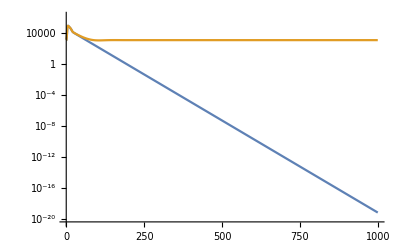

```mathematica
LogPlot[{v[t]/.soln1,v[t]/.soln2},{t,0,tmax},PlotRange->All]
```

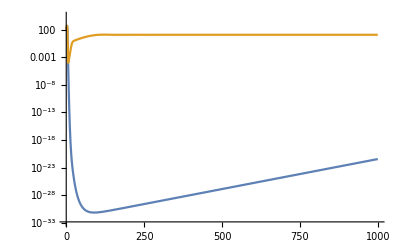

```mathematica
LogPlot[{n0[t]/.soln1,n0[t]/.soln2},{t,0,tmax},PlotRange->All]
```

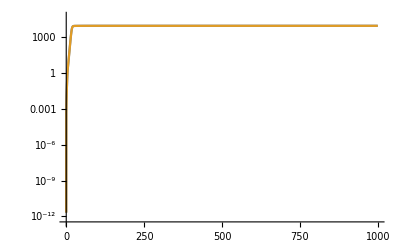

```mathematica
LogPlot[{n1[t]/.soln1,n1[t]/.soln2},{t,0,tmax},PlotRange->All]
```

Effectiveness model, stationary state

```mathematica
FeffRule=Feff->k/(b-1)(a b-1)/(1-a b ϵavg);
n0Rule=n0->Evaluate[(1-a b ϵavg)/(1-ϵavg)(Kpop μ)/(b f)(f-Feff)/(a μ + Feff)/.FeffRule//Simplify];
niRule=n[i]->Evaluate[(1-ϵavg)/(1 - a b ϵavg)((a b - 1)α n0)/(a(b-1)(1-ϵavg)-(1-ϵ[i])(a b - 1))/.n0Rule//Simplify];
aRule=a->1-ns α;
constraint=(Sum[n[i],{i,1,ns}]==(a b - 1)/(1-a b ϵavg)n0);
```

Let’s consider some realistic parameters.

```mathematica
realisticParameters1={f->1.0,b->50,k->0.001,α->0.0001,μ->5.0,g->0.001,Kpop->1*^10,ns->10};
```

Generate some effectivenesses.

```mathematica
eParameters=RandomReal[{0.001,0.01},(ns/.realisticParameters1)];
eParameterRules=MapIndexed[ϵ[#2[[1]]]->#1&,eParameters];
```

Use the constraint to fix ϵ_avg.

```mathematica
eavgEquation=Sum[1/(ϵ[i](a b-1)-ϵavg a (b-1)+(1-a)),{i,1,ns}]==1/(α(1-ϵavg));
```

```mathematica
eavgEquation/.aRule/.realisticParameters1/.eParameterRules;
```

```mathematica
eavgSolns=NSolve[eavgEquation/.aRule/.realisticParameters1/.eParameterRules,ϵavg]
```

{{ϵavg→0.00798523},{ϵavg→0.00262706},{ϵavg→0.00102608}}

```mathematica
a b ϵavg/.aRule/.realisticParameters1/.eavgSolns
```

{0.398862,0.131221,0.0512525}

Check that the constraint is (approximately) satisfied.

```mathematica
((constraint/.niRule/.n0Rule/.aRule/.realisticParameters1/.eParameterRules)/.(a_==b_)->(a-b)/(a+b))/.eavgSolns
```

{7.18184×10^-8,-1.7221×10^-8,6.37246×10^-11}

```mathematica
stationaryPopulations=Table[n[i]/.niRule/.aRule,{i,1,(ns/.realisticParameters1)}]/.realisticParameters1/.eParameterRules/.eavgSolns
```

{{-1.30561×10^7,-5.06511×10^6,9.94513×10^9,-2.87184×10^6,-3.61005×10^7,-3.73025×10^6,-9.03382×10^6,-4.96958×10^6,-5.66961×10^6,-5.64536×10^6},{5.22273×10^6,1.41425×10^7,3.72972×10^6,-1.25034×10^7,4.1609×10^6,9.75411×10^9,6.35368×10^6,1.49442×10^7,1.08997×10^7,1.09904×10^7},{3.68297×10^6,6.63252×10^6,2.87227×10^6,9.74601×10^9,3.12133×10^6,1.24728×10^7,4.21154×10^6,6.80366×10^6,5.8205×10^6,5.84626×10^6}}

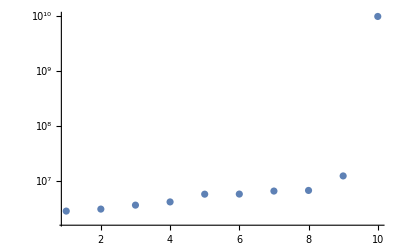

```mathematica
ListLogPlot[Sort[stationaryPopulations[[3]]],PlotRange->All]
```

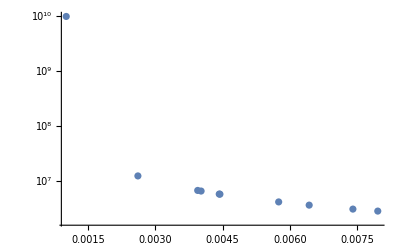

```mathematica
ListLogPlot[{Transpose[{eParameters,stationaryPopulations[[3]]}]},PlotRange->All]
```

## Small deviations around average efectiveness

```mathematica
Series[(Feff/.FeffRule),{ϵavg,0,1}]
```

((-1+a b) k)/(-1+b)+(a b (-1+a b) k ϵavg)/(-1+b)+O[ϵavg]^2

```mathematica
Series[(n0/.n0Rule),{ϵavg,0,1}]//Simplify
```

(((-1+b) f+k-a b k) Kpop μ)/(b f ((-1+a b) k+a (-1+b) μ))+((-1+a b) Kpop μ (k ((-1+a b)^2 k-a (-1+b) μ)-(-1+b) f ((-1+2 a b) k+a (-1+b) μ)) ϵavg)/(b f ((-1+a b) k+a (-1+b) μ)^2)+O[ϵavg]^2

```mathematica
niApprox=Normal[Series[Evaluate[(n[i]/.niRule)/.ϵavg->(ϵ0 + ξ ϵavg)/.ϵ[i]->(ϵ0 + ξ ϵ[i])],{ξ,0,1}]//Simplify]
```

((-1+a b) Kpop α ((-1+a b) k+(-1+b) f (-1+a b ϵ0)) μ)/((-1+a) b f (-1+ϵ0) (k-a b k+a (-1+b) (-1+a b ϵ0) μ))+1/(b f (-1+a+ϵ0-a ϵ0)^2)(-1+a b) Kpop α μ ξ (-((-1+a) a (-1+b) b (-1+a b) k (-1+ϵ0) ϵavg (f+a μ))/((-1+a b) k-a (-1+b) (-1+a b ϵ0) μ)^2+(((-1+a b) k+(-1+b) f (-1+a b ϵ0)) (a (-1+b) ϵavg+(1-a b) ϵ[i]))/(k-a b k+a (-1+b) (-1+a b ϵ0) μ))

```mathematica
niϵiApprox=Normal[Series[Evaluate[(n[i] ϵ[i]/.niRule)/.ϵavg->(ϵ0 + ξ ϵavg)/.ϵ[i]->(ϵ0 + ξ ϵ[i])],{ξ,0,1}]//Simplify]
```

((-1+a b) Kpop α ϵ0 ((-1+a b) k+(-1+b) f (-1+a b ϵ0)) μ)/((-1+a) b f (-1+ϵ0) (k-a b k+a (-1+b) (-1+a b ϵ0) μ))+1/(b f (-1+a+ϵ0-a ϵ0)^2)(-1+a b) Kpop α μ ξ ((ϵ0 ((-1+a b) k+(-1+b) f (-1+a b ϵ0)) (a (-1+b) ϵavg+(1-a b) ϵ[i]))/(k-a b k+a (-1+b) (-1+a b ϵ0) μ)-(-1+a+ϵ0-a ϵ0) (-(a (-1+b) b (-1+a b) k ϵ0 ϵavg (f+a μ))/((-1+a b) k-a (-1+b) (-1+a b ϵ0) μ)^2+(((-1+a b) k+(-1+b) f (-1+a b ϵ0)) ϵ[i])/(k-a b k+a (-1+b) (-1+a b ϵ0) μ)))

```mathematica
Sum[niϵiApprox,{i,1,N}]
```

∑_(i=1)^N (((-1+a b) Kpop α ϵ0 ((-1+a b) k+(-1+b) f (-1+a b ϵ0)) μ)/((-1+a) b f (-1+ϵ0) (k-a b k+a (-1+b) (-1+a b ϵ0) μ))+1/(b f (-1+a+ϵ0-a ϵ0)^2)(-1+a b) Kpop α μ ξ ((ϵ0 ((-1+a b) k+(-1+b) f (-1+a b ϵ0)) (a (-1+b) ϵavg+(1-a b) ϵ[i]))/(k-a b k+a (-1+b) (-1+a b ϵ0) μ)-(-1+a+ϵ0-a ϵ0) (-(a (-1+b) b (-1+a b) k ϵ0 ϵavg (f+a μ))/((-1+a b) k-a (-1+b) (-1+a b ϵ0) μ)^2+(((-1+a b) k+(-1+b) f (-1+a b ϵ0)) ϵ[i])/(k-a b k+a (-1+b) (-1+a b ϵ0) μ))))

Checking some analytical calculations

```mathematica
tmp1=Solve[(g v-FF)/k==(b(1-α)-1)/(1-b η),v][[1]]//Simplify
```

{v→(FF-k+b k-b k α-b FF η)/(g-b g η)}

```mathematica
tmp2=Solve[(((f1/f0 FF-k-g v η)(b(1-α)-1)/(1-b η)+α g v==0)/.tmp1//Simplify),FF][[1]]//Simplify
```

{FF→(f0 k (1+b (-1+α)) (-1+α+η))/((-1+b η) (f1 (1+b (-1+α))-f0 (α+η-b η)))}

```mathematica
tmp2/.f1->f0/.α->(1-a)//Simplify
```

{FF→(k-a b k)/((-1+b) (-1+b η))}

```mathematica
tmp2/.f1->f0//Simplify
```

{FF→(k (1+b (-1+α)))/((-1+b) (-1+b η))}

```mathematica
FF-k(b(1-α)-1)/((b-1)(1-b η))/.tmp2//Simplify
```

((f0-f1) k (1+b (-1+α))^2)/((-1+b) (-1+b η) (f1 (1+b (-1+α))-f0 (α+η-b η)))

```mathematica
tmp3=μ/b(1-b η)/(μ(a-η)+FF(1-η+b η(a-1)))
```

((1-b η) μ)/(b (FF (1-η+(-1+a) b η)+(a-η) μ))

```mathematica
Series[(tmp3/.(tmp2/.f1->f0/.α->(1-a)//Simplify)//Simplify),{k,0,1}]
```

(1-b η)/(b (a-η))-((-1+a b) (1-η-b η+a b η) k)/((-1+b) b (a-η)^2 μ)+O[k]^2